```mathematica
(*Load the packages*)
<<PhysicalConstants`;
<<Units`;

(*Define physical constants*)
alpha=FineStructureConstant;
c=SpeedOfLight//First;
G=GravitationalConstant//First;
eAu=ElectronCharge//First;
h=PlanckConstant//First;
hbar=QuantityMagnitude[Quantity[1,"ReducedPlanckConstant"],"J*s"];

(*Conversion factors*)
CNu=(4*Pi*alpha)^(1/2)/eAu;
kgToEv=c^2/eAu;
mToEvMinus1=eAu/hbar/c;
JToEv=1/eAu;
sToEvMinus1=eAu/(hbar);
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
(*Define constants*)
MPl=Sqrt[hbar*c/G]*kgToEv; (*Planck mass in eV*)
gStar=100; (*Effective degrees of freedom*)
TStar=100*10^9; (*Electroweak scale in eV*)

(*Compute Hubble rate H* *)
HStar=Sqrt[(8*Pi^3*gStar*TStar^4)/(90*MPl^2)];

(*Compute beta=100*H* *)
β=100*HStar;

(*Compute bubble separation R* *)
RStar=(8*Pi)^(1/3)*vW/β;

(*Total energy density*)
ρTot=(Pi^2/30)*gStar*TStar^4;
```

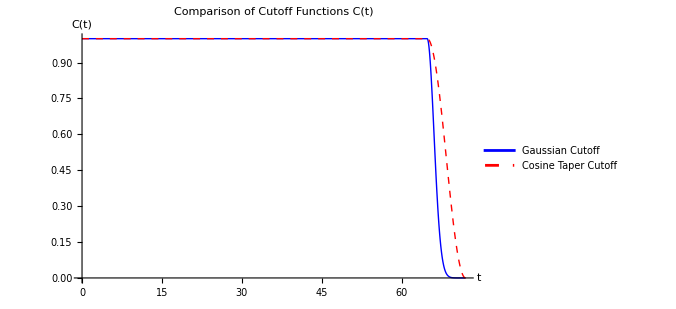

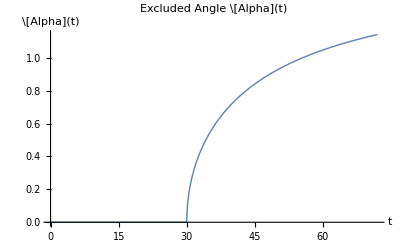

```mathematica
(*Define parameters*)
d=60; (*Bubble separation*)
α=1.2; (*Cutoff factor*)
τ=α*d;(*Cutoff time*)
vW=1;(*Bubble wall velocity*)

(*Define cutoff function C(t) with continuous transition*)
CutOff[t_?NumericQ,τ_?NumericQ]:=Piecewise[{{1,0<=t<=0.9*τ},{Exp[-(t-0.9*τ)^2/(0.025*τ)^2],0.9*τ<=t<=τ}}]
CutOffCos[t_?NumericQ,τ_?NumericQ]:=Which[0<=t<=0.9*τ,1,0.9*τ<t<=τ,(1+Cos[Pi*(t-0.9*τ)/(0.1*τ)])/2,True,0]

(*Plot both cutoff functions*)
Plot[{CutOff[t,τ],CutOffCos[t,τ]},{t,0,τ},PlotLabel->"Comparison of Cutoff Functions C(t)",AxesLabel->{"t","C(t)"},PlotRange->All, PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}},PlotLegends->{"Gaussian Cutoff","Cosine Taper Cutoff"}, ImageSize->500]

(*Define excluded angle α(t)*)
ExcludeAngle[t_?NumericQ,d_?NumericQ,vW_?NumericQ]:=If[t>d/(2 vW),ArcCos[d/(2 vW t)],0]

(*Plot the excluded angle α(t)*)
Plot[ExcludeAngle[t,d,vW],{t,0, τ},PlotLabel->"Excluded Angle \\[Alpha](t)",AxesLabel->{"t","\\[Alpha](t)"},PlotRange->All,Exclusions->None,PlotStyle->Thick]
```

```mathematica
(*Txx function*)innerTxx[t_?NumericQ,ω_?NumericQ,ψ_?NumericQ,vW_?NumericQ,d_?NumericQ]:=NIntegrate[Sin[θ]^3*Cos[ω*Cos[ψ]*vW*t*Cos[θ]+1/2*ω*Cos[ψ]*d]*(BesselJ[0,ω*Sin[ψ]*vW*t*Sin[θ]]-BesselJ[2,ω*Sin[ψ]*vW*t*Sin[θ]]),{θ,0,Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->5,AccuracyGoal->5];
TxxUnscaled[ω_?NumericQ,ψ_?NumericQ,vW_?NumericQ,d_?NumericQ,τ_?NumericQ]:=NIntegrate[t^3*CutOff[t,τ]*Exp[I*ω*t]*innerTxx[t,ω,ψ,vW,d],{t,0,τ},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->4,AccuracyGoal->4]
```

```mathematica
(*Tyy function*)innerTyy[t_?NumericQ,ω_?NumericQ,ψ_?NumericQ,vW_?NumericQ,d_?NumericQ]:=NIntegrate[Sin[θ]^3*Cos[ω*Cos[ψ]*vW*t*Cos[θ]+1/2*ω*Cos[ψ]*d]*(BesselJ[0,ω*Sin[ψ]*vW*t*Sin[θ]]+BesselJ[2,ω*Sin[ψ]*vW*t*Sin[θ]]),{θ,0,Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->5,AccuracyGoal->5];
TyyUnscaled[ω_?NumericQ,ψ_?NumericQ,vW_?NumericQ,d_?NumericQ,τ_?NumericQ]:=NIntegrate[t^3*CutOff[t,τ]*Exp[I*ω*t]*innerTyy[t,ω,ψ,vW,d],{t,0,τ},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->4,AccuracyGoal->4]
```

```mathematica
(*Tzz function*)innerTzz[t_?NumericQ,ω_?NumericQ,ψ_?NumericQ,vW_?NumericQ,d_?NumericQ]:=NIntegrate[2*Sin[θ]*Cos[θ]^2*Cos[ω*Cos[ψ]*vW*t*Cos[θ]+1/2*ω*Cos[ψ]*d]*BesselJ[0,ω*Sin[ψ]*vW*t*Sin[θ]],{θ,0,Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->5,AccuracyGoal->5];
TzzUnscaled[ω_?NumericQ,ψ_?NumericQ,vW_?NumericQ,d_?NumericQ,τ_?NumericQ]:=NIntegrate[t^3*CutOff[t,τ]*Exp[I*ω*t]*innerTzz[t,ω,ψ,vW,d],{t,0,τ},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->4,AccuracyGoal->4]
```

```mathematica
(*Txz function*)innerTxz[t_?NumericQ,ω_?NumericQ,ψ_?NumericQ,vW_?NumericQ,d_?NumericQ]:=NIntegrate[-2*Sin[θ]^2*Cos[θ]*Sin[ω*Cos[ψ]*vW*t*Cos[θ]+1/2*ω*Cos[ψ]*d]*BesselJ[1,ω*Sin[ψ]*vW*t*Sin[θ]],{θ,0,Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->5,AccuracyGoal->5];
TxzUnscaled[ω_?NumericQ,ψ_?NumericQ,vW_?NumericQ,d_?NumericQ,τ_?NumericQ]:=NIntegrate[t^3*CutOff[t,τ]*Exp[I*ω*t]*innerTxz[t,ω,ψ,vW,d],{t,0,τ},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->4,AccuracyGoal->4]
```

```mathematica
(*Unscaled dE/dω*)
TijUnscaled[ω_, ψ_, vW_, d_, τ_]:=TxxUnscaled[ω,ψ,vW,d,τ]*Cos[ψ]^2-TyyUnscaled[ω,ψ,vW,d,τ]+TzzUnscaled[ω,ψ,vW,d,τ]*Sin[ψ]^2-2*TxzUnscaled[ω,ψ,vW,d,τ]*Sin[ψ]*Cos[ψ];
dEperdωUnscaled[ω_?NumericQ,vW_?NumericQ,d_?NumericQ,τ_?NumericQ]:=Monitor[NIntegrate[Sin[ψ]*Abs[TijUnscaled[ω, ψ, vW, d, τ]]^2,{ψ,0,Pi},Method->{"GlobalAdaptive","MaxErrorIncreases"->100,"MaxRecursion"->25},PrecisionGoal->4,AccuracyGoal->3],Column[{ProgressIndicator[ψ,{0,Pi}],Row[{"ω = ",NumberForm[ω,{6,4}],", ψ = ",NumberForm[ψ,{6,4}]}]}]]
```

```mathematica
(*Higgs fields in C2HDM*)
h1[v1_, ξ_, L_]:=v1/2*(1+Tanh[ξ/L])
h2[v2_, ξ_, L_]:=v2/2*(1+Tanh[ξ/L])
θ[Δθ_, ξ_, L_]:=Δθ/2*(1+Tanh[ξ/L])
σ[v1_, v2_, ξ_, L_]:=D[h1[v1, ξ, L], ξ]^2+D[h2[v2, ξ, L], ξ]^2+h2[v2, ξ, L]^2*D[θ[Δθ, ξ, L], ξ]^2
σ[v1, v2, ξ, L]/.ξ->0
```

v1^2/(4 L^2)+v2^2/(4 L^2)+(v2^2 Δθ^2)/(16 L^2)

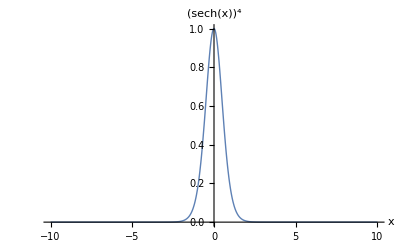

```mathematica
Plot[Sech[x]^4,{x,-10,10},PlotLabel->TraditionalForm[sech[x]^4],AxesLabel->{"x",None},PlotRange->All,Exclusions->None,PlotStyle->Thick]
```